```mathematica
S[q_] :=Simplify[Plus @@ (Cot[Pi #/q]^2 & /@ Select[Range[q-1],GCD[#,q]==1&])];
```

```mathematica
Phi2[q_] := q^2 Times @@ ((1 - 1/#[[1]]^2)&/@ FactorInteger[q]);
```

```mathematica
SBM[q_?IntegerQ] := 1/3 Phi2[q]-EulerPhi[q];
```

```mathematica
SBM[22071945]
```

135744984254976

```mathematica
FullSimplify[S[100]]//Timing
```

{63.2377,2360}

```mathematica
SBM[100]//Timing
```

{0.00014,2360}

```mathematica
SMdata={#,SBM[#]}& /@ Range[10,100000];
```

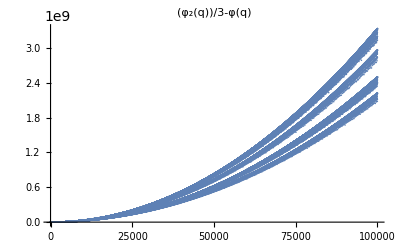

```mathematica
ListPlot[SMdata,PlotLabel->Subscript[φ,2][q]/3-φ[q]]
```

```mathematica
SBM[9]
```

18

```mathematica
9^2(1-1/9)/3 -9(1-1/3)
```

18

```mathematica
Table[{q,SBM[q]},{q,2,10}]
```

{{2,0},{3,2/3},{4,2},{5,4},{6,6},{7,10},{8,12},{9,18},{10,20}}

```mathematica
6^2(1-1/9)(1-1/4)/3 = (3-1)(3+1)(2-1)(2+1)/3
```

8

```mathematica
Table[Phi2[q]/3,{q,3,20}]
```

{8/3,4,8,8,16,16,24,24,40,32,56,48,64,64,96,72,120,96}

```mathematica
SBM[2^64+1]
```

113427455638803936117726648213506949120

```mathematica
SBM[2^64]
```

85070591730234615856620279821087277056

```mathematica
SBM[2^128+1]
```

38597363079105398474523661669562625103150274109036501299425668761748925317120

```mathematica
SBM[Prime[200000]]
```

2521122091602

```mathematica
SBM[Prime[200000]+1]
```

1580590852608